```mathematica
SetDirectory[NotebookDirectory[]];
Get["LearningNewtonsMethod/LearningNewtonsMethod.m"];
SetOptions[EvaluationNotebook[],Background->None]
SetOptions[SelectedNotebook[], 
         System`BackgroundAppearance -> ConvertImageToFullyScaledNinePatch[-Graphics-]];
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideZero"}]]
Grid[{{ GoBack[slidePrima, 0], GoHomepage[slidePrima], GoForward[slideLegenda, 1]}}, ItemSize->Fit]
```

-Graphics- | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideLegendaButtonDataHyperlinkHyperlinkActive

# -Graphics- | | | | Metodo di Newton | | | | | | | | | -Graphics- Anna Avena Matteo Sanfelici Giulia Cantini Roberto Ferraro Nicola Mainetti Matematica Computazionale Anno Accademico 2017/2018

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideLegenda"}]]
Grid[{{ GoBack[slideZero, 1], GoHomepage[slidePrima], GoForward[slidePrima, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideZeroButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslidePrimaButtonDataHyperlinkHyperlinkActive

## Legenda

In questo progetto alcune parole e concetti chiave saranno presentati sempre con gli stessi colori

Le funzioni saranno sempre blu
Gli zeri delle funzioni saranno sempre rossi
Le approssimazioni di questi saranno sempre verdi
La tolleranza dei metodi sarà sempre viola

Quando incontri questi colori saprai subito di cosa si sta parlando

## Prerequisiti

Prima di iniziare a studiare questo nuovo argomento assicurati di conoscere bene:

Cos’è una Funzione

Una funzione è una relazione tra due insiemi, chiamati dominio e codominio della funzione, che associa a ogni elemento del dominio uno e un solo elemento del codominio.

Cos' è un’Equazione associata ad una funzione.

L’equazione associata ad f(x) è f(x) = 0.

Derivate in un punto

La derivata di una funzione in un punto z è il limite del rapporto incrementale di quella funzione calcolata in z. Inoltre corrisponde al coefficente angolare della retta tangente al grafico della funzione nel punto di ascissa z.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slidePrima"}]]
Grid[{{ GoBack[slideLegenda, 1], GoHomepage[slidePrima], GoForward[slideSeconda, 1]}}, ItemSize->Fit]
```

-Graphics-jim2n_shmslideLegendaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSecondaButtonDataHyperlinkHyperlinkActive

## Outline

Presentazione del problema

Metodo di bisezione

Metodo delle secanti

Metodo di Newton

Funzionamento

Teoria

```mathematica
CellPrint[Cell["", "", CellTags->{"slideSeconda"}]]
Grid[{{ GoBack[slidePrima, 1], GoHomepage[slidePrima], GoForward[slideTerza, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslidePrimaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideTerzaButtonDataHyperlinkHyperlinkActive

## Problema: ricerca di uno zero di una funzione

Ti sei mai chiesto come fa la calcolatrice a calcolare √2?

Notiamo che (√2)^2-2=0,
quindi √2 è uno zero della funzione f(x)=x^2-2.

In altre parole,calcolare √2, è equivalente a definire f(x) e cercarne uno zero.

Come calcolare √α

In generale se voglio calcolare √α (con α>0), posso considerare f(x)=x^2-α.

Uno zero di f(x)  è √α.

Come calcolare α^(1/n)

Ancora più in generale, se voglio calcolare α^(1/n)posso considerare f(x) = x^n-α.
Uno zero di f(x)  è α^(1/n).

La calcolatrice definisce f(x)=x^2-2 e cerca gli zeri di f(x). 

La calcolatrice inoltre  ci restituisce una rappresentazione decimale di √2

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTerza"}]]
Grid[{{ GoBack[slideSeconda, 1], GoHomepage[slidePrima], GoForward[slideQuarta, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSecondaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideQuartaButtonDataHyperlinkHyperlinkActive

## Ma come si trova la rappresentazione decimale di uno zero di f(x)?

Questo problema potrebbe essere irrisolubile se il numero cercato fosse irrazionale poiché avrebbe infinite cifre decimali.

Ad esempio, √2 è un numero reale irrazionale, quindi con infinite cifre decimali dopo la virgola, e la calcolatice lo rappresenta come 1,4142...

Infatti è sempre possibile ottenere un’approssimazione anche con molte cifre decimali di un qualsiasi numero.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuarta"}]]
Grid[{{ GoBack[slideTerza, 1], GoHomepage[slidePrima], GoForward[slideQuinta, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideTerzaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideQuintaButtonDataHyperlinkHyperlinkActive

## Theorema di Bolzano

```mathematica
Bolzano[]
```

Notiamo che la funzione f(x) = x^2-2 è continua

 e che f calcolata in a = 1 è negativa .

Inoltre notiamo che f calcolata in b = 2 è positiva .

Ciò che abbiamo appena osservato sono le ipotesi del Teorema di Bolzano.



Quindi possiamo esser certi che tra 1 e 2 è compreso un suo zero .

Teorema di Bolzano

Data una funzione f (x) continua in un intervallo [a, b] tale che f (a) f (b) < 0 allora 
∃ c ∈ [a, b] tale che f (c) =0.

ll ragionamento appena affrontato vale più in generale per qualunque funzione f(x) continua in un intervallo [a,b], che assume valori di segno opposto in a e b.

Vedremo ora 3 differenti metodi numerici per calcolare un valore approssimato di √2.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuinta"}]]
Grid[{{ GoBack[slideQuarta, 1], GoHomepage[slidePrima], GoForward[slideSesta, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideQuartaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSestaButtonDataHyperlinkHyperlinkActive

## Metodo di bisezione

Partendo dall’osservazione che f(x) = x^2- 2 calcolata in 1 è negativa mentre calcolata in 2 è positiva, pensiamo di trovare un’approssimazione di √2 nel valore medio tra 1 e 2

(1 + 2)/2= 1,5 = x_1

```mathematica
BisectionInteractive[0,0]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta"}]]
Grid[{{ GoBack[slideQuinta, 1], GoHomepage[slidePrima], GoForward[slideSesta2, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideQuintaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSesta2ButtonDataHyperlinkHyperlinkActive

Verifichiamo ora che la funzione calcolata nell’approssimazione appena ottenuta x_1 assuma un valore vicino a 0;

f(1,5) = 1,5^2 - 2 = 2,25 - 2 = 0,25

Poiché f calcolata in 1,5 è positiva mentre, come detto, calcolata in 1 è negativa possiamo dedurre che lo zero della funzione sia tra 1 e 1,5 ed assumerne come seconda approssimazione x_2 il valor medio tra 1 e 1,5

TODO GRAFICO PASSO PASSO?

Ripetiamo il ragionamento (la parte sottolineata) dimezzando di volta in volta l’intervallo considerato ed otteniamo una successione di approssimazioni di √2 come mostrato in figura nella slide successiva;

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta2"}]]
Grid[{{ GoBack[slideSesta, 1], GoHomepage[slidePrima], GoForward[slideSesta3, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSestaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSesta3ButtonDataHyperlinkHyperlinkActive

## Slide

Contuiniamo a cercare approssimazioni fin quando la differenza tra le ultime due trovate è minore di 0,0000001   COERENTE CON A-B (?????)

```mathematica
BisectionInteractive[0,1]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta3"}]]
Grid[{{ GoBack[slideSesta2, 1], GoHomepage[slidePrima], GoForward[slideSesta4, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSesta2ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSesta4ButtonDataHyperlinkHyperlinkActive

Possiamo sfruttare lo stesso metodo che abbiamo usato per trovare un’approssimazione di √2per ricercare uno zero c di una qualsiasi funzione all’interno di un intervallo [a,b] purché f assuma in a ed in b valori di segno opposto.

```mathematica
BisectionInteractive[1,1]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSesta4"}]]
Grid[{{ GoBack[slideSesta3, 1], GoHomepage[slidePrima], GoForward[slideSettima, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSesta3ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSettimaButtonDataHyperlinkHyperlinkActive

Se abbiamo a che fare con numeri irrazionali potremmo non ottenere mai c ma sole sue approssimazioni.

In questo caso, o quando il numero ha troppe cifre decimali, decidiamo di essere soddisfatti quando l’ultima approssimazione x_i trovata non sia più grande o più piccola di c di un certo valore di tolleranza τ.

Poiché non conosciamo il valore di c  allora ci fermeremo quando la differenza tra x_i e x_(i-1) sara’ piu’ piccola di τ.

```mathematica
AlgoBisez[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSettima"}]]
Grid[{{ GoBack[slideSesta4, 1], GoHomepage[slidePrima], GoForward[slideSettima2, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSesta4ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSettima2ButtonDataHyperlinkHyperlinkActive

## Metodo delle secanti

Esistono altri metodi per calcolare √2?

Osservando il grafico qui sotto ci rendiamo subito conto che la retta secante f(x) nei punti (1;-1) e (2;2) interseca l’asse delle ascisse nel punto (0;1,OverBar[3]).

```mathematica
SecantInteractive[0,0]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSettima2"}]]
Grid[{{ GoBack[slideSettima, 1], GoHomepage[slidePrima], GoForward[slideSettima3, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSettimaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSettima3ButtonDataHyperlinkHyperlinkActive

## Metodo delle secanti - continuo

1,OverBar[3] è un approssimazione di √2 migliore della prima che ci aveva restituito il metodo di bisezione, che era 1,5 ; 

Vediamo cosa succede reiterando il metodo:

```mathematica
SecantInteractive[0,1]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideSettima3"}]]
Grid[{{ GoBack[slideSettima2, 1], GoHomepage[slidePrima], GoForward[slideOttava, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSettima2ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideOttavaButtonDataHyperlinkHyperlinkActive

Abbiamo quindi scoperto un’altra tecnica per la ricerca dell’approssimazione dello zero.

Sia P = (x_1, y_1) il punto di intersezione tra l’asse x e la retta che passa per i punti (a, f(a)) e (b, f(b)).
Assumiamo come valore approssimato dello zero il valore x_1,ovvero l’ascissa del punto P.

Le coordinate di P sono le soluzioni del sistema

```mathematica
Piecewise[{{y=0, }, {(x-a)/(b-a) = (y - f(a))/(f(b) - f(a)), }}]
```

0

Si ottiene x_1 = a-(f(a)(b-a))/(f(b)-f(a))

```mathematica
SecantInteractive[1,1]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideOttava"}]]
Grid[{{ GoBack[slideSettima3, 1], GoHomepage[slidePrima], GoForward[slideNona, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideSettima3ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideNonaButtonDataHyperlinkHyperlinkActive

## Algoritmo

```mathematica
AlgoSec[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideNona"}]]
Grid[{{ GoBack[slideOttava, 1], GoHomepage[slidePrima], GoForward[slideNona2, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideOttavaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideNona2ButtonDataHyperlinkHyperlinkActive

### METODO DI NEWTON

Il metodo della bisezione e quello delle secanti si sono rivelati 2 buoni metodi per approssimare √2 ma non sono i più “veloci”.

Isaac Newton (1642-1727) riuscì a trovare un metodo in grado di trovare approssimazioni dello zero di una funzione con la precisione voluta in molti meno passaggi.

TODO IMMAGINE DI NEWTON GIF

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideNona2"}]]
Grid[{{ GoBack[slideNona, 1], GoHomepage[slidePrima], GoForward[slideDecima, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideNonaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideDecimaButtonDataHyperlinkHyperlinkActive

L’idea di Newton è stata quella di considerare un’approssimazione x_i del valore cercato e non un intervallo come gli altri metodi.

Newton trova r retta tangente al grafico della funzione nel punto di ascissa x_i .

Calcola poi la successiva approssimazione x_(i+1) come l’ascissa del punto di intersezione tra la tangente r e l’asse delle x.

Osservando la finestra qui sotto è più facile capire il funzionamento del metodo:

```mathematica
NewtonInteractive[1,1]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDecima"}]]
Grid[{{ GoBack[slideNona2, 1], GoHomepage[slidePrima], GoForward[slideUndici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideNona2ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideUndiciButtonDataHyperlinkHyperlinkActive

## Metodo di Newton (o delle tangenti) :

La retta r ha coefficiente angolare f ‘(x_i) e passa per il punto  (x_i, f(x_i)). 

Ha quindi equazione

y - f(x_i) = f’(x_i) (x - x_i)

L’intersezione tra r e l’asse delle x è la soluzione del sistema:

```mathematica
Piecewise[{{y = 0, }, {y - f (a) = f '(a)(x-a), }}]
```

0

Si ottiene x_1 = a - (f(a))/(f'(a))

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideUndici"}]]
Grid[{{ GoBack[slideDecima, 1], GoHomepage[slidePrima], GoForward[slideUndici2, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideDecimaButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideUndici2ButtonDataHyperlinkHyperlinkActive

### Algoritmo

```mathematica
AlgoNewton[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideUndici2"}]]
Grid[{{ GoBack[slideUndici, 1], GoHomepage[slidePrima], GoForward[slideDodici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideUndiciButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideDodiciButtonDataHyperlinkHyperlinkActive

## Confronto tra i tre metodi

```mathematica
MethodsComparison[]
```

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideDodici"}]]
Grid[{{ GoBack[slideUndici2, 1], GoHomepage[slidePrima], GoForward[slideTredici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideUndici2ButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideTrediciButtonDataHyperlinkHyperlinkActive

## Limiti del metodo di Newton

Il metodo delle tangenti, o metodo di Newton, può presentare delle problematiche.

Nell’ esempio qui sotto si può notare che il metodo dà come seconda approssimazione dello zero un valore esterno al dominio della funzione.

Quindi non è possibile disegnare la seconda tangente per trovare una terza approssimazione.

```mathematica
FirstExample[]
```

In generale, se il metodo dà un’approssimazione esterna al dominio della funzione non è piu possibile trovare successive approssimazioni ed il metodo perde di significato.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideTredici"}]]
Grid[{{ GoBack[slideDodici, 1], GoHomepage[slidePrima], GoForward[slideQuattordici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideDodiciButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive

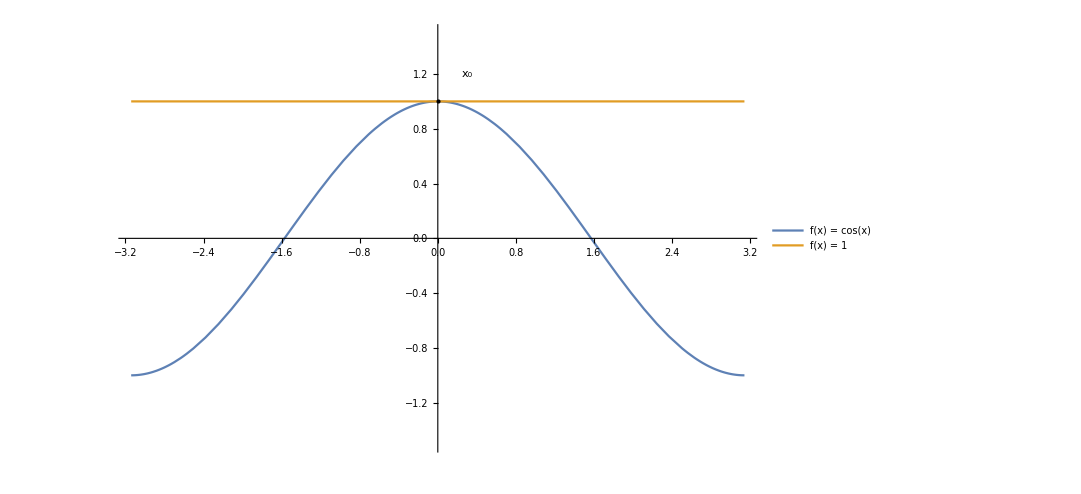

In quest’altro esempio invece possiamo notare che non è possibile calcolare neanche una prima approssimazione dello zero x_1 = a - (f(a))/(f'(a)) poiché  f ’ (a) = 0.

Geometricamente si vede che la retta tangente al punto (0,1) è parallela all’asse delle x e quindi non lo incontra mai.

Quindi anche nel caso in cui per una approssimazione x_i si ha f’(x_i) = 0, non è piu possibile trovare successive approssimazioni ed il metodo perde di significato.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuattordici"}]]
Grid[{{ GoBack[slideTredici, 1], GoHomepage[slidePrima], GoForward[slideQuindici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideTrediciButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideQuindiciButtonDataHyperlinkHyperlinkActive

Per ovviare a questi due possibili problemi possiamo limitarci ad usare questo metodo con opportune restrizioni:

Per prima cosa, chiediamo che le approssimazioni dello zero calcolate col metodo non cadano fuori dal dominio della funzione.

Inoltre chiediamo che la funzione ammetta derivata prima continua e che di volta in volta non si annulli nei punti assunti come approssimazione.

```mathematica
CellPrint[Cell["", "", CellTags -> {"slideQuindici"}]]
Grid[{{ GoBack[slideQuattordici, 1], GoHomepage[slidePrima], GoForward[slideSedici, 1]}}, ItemSize -> Fit]
```

-Graphics-jim2n_shmslideQuattordiciButtonDataHyperlinkHyperlinkActive | -Graphics-jim2n_shmslidePrimaButtonData | -Graphics-jim2n_shmslideSediciButtonDataHyperlinkHyperlinkActive

Con le restrizioni dette il metodo può produrre una sequenza di “approssimazioni” lunga quanto vogliamo.

Non siamo però certi che queste “approssimazioni” siano realmente prossime allo zero cercato né che gli convergeranno mai. 

Se sei curioso di sapere sotto quali restrizioni siamo sicuri che il metodo di Newton restituisca una soluzione vicina allo zero e perché ciò accade premi qua sotto!

APRI LA TEORIA PREMENDO SULLA FRECCIA

Teorema 1

Data l’ equazione f (x) = 0, sia c un suo zero ed x_1 un suo valore approssimato; 
posto

                                           F(x) = x - (f (x))/(f ' (x))

e calcolata la successione


				(x_(i+1))_ = F(x_i)_(con i = 1,2,...)


se esiste un numero k < 1 tale che nell’intervallo che contiene i punti x_1, x_2, … , c risulta


				| F’ (x) | ≤  k 

allora

				lim_(i→+∞) x_1= c
				
				
Dimostrazione

Per prima cosa proviamo F(c) = c

                                         F(c) = c-(f (c))/(f ' (c))

ed essendo c una radice dell’equazione f (x) = 0 segue che f (c) = 0 e quindi 


                                         F(c) = c

Andiamo ora  a calcolare la distanza fra x_2 e c

                                                   x_2- c = F(x_1) - F(c)

Vogliamo applicare il teorema di Lagrange (o del valor medio) alla funzione F per ottenere 

                                        x_2- c= (x_1- c) F'(x)

con x appartenente all’intervallo [ x_1, c ].

Per fare ciò dobbiamo dimostrare che la funzione F(x) rispetti le ipotesi del teorema di Lagrange.

Per non appesantire la dimostrazione proveremo questo nel lemma successivo al teorema.

Usando l’ipotesi | F’ (x) | ≤ k abbiamo

				|x_2 - c | ≤ | x_1 - c | k

iterando il ragionamento

				|x_(i+1)- c | ≤ |x_i - c | (k^i)
				
ed essendo k < 1 si ha

				lim_(i→ +∞) |x_(i+1)-c| = 0
e quindi

				lim_(i→ +∞) |x_i|  = c

									c.v.d.

Lemma

La funzione F(x) del teorema precedente rispetta le ipotesi del teorema di Lagrange nell’intervallo che contiene i punti x_1,x_2, … , c .

Dimostrazione

Ricordiamo che le ipotesi del teorema di Lagrange sono: 

la funzione continua e 

la funzione derivabile in tutto l’intervallo al più escludendo gli estremi.


				F(x) = x-(f(x))/(f'(x))
				

f(x) e’ stata supposta continua all’inizio di questo paragrafo.

Analogamente f’(x) e’ stata supposta continua e non nulla nei punti che ci interessano.


Quindi (f(x))/(f'(x)) è una funzione continua e lo è anche la funzione F(x) in quanto somma di funzioni continue.

                                               F'(x) =1-{(f'(x)^2-f(x)f'(x))/(f'(x)^2) }

                                               
                                               
                                                           = 1- 1+{ (f(x)f'(x))/(f'(x)^2) }


                                                     
= { (f(x)f'(x))/(f'(x)^2)  }

                                               
 F(x) è derivabile se (f(x)f'(x))/(f'(x)^2) è continua nell’intervallo che ci interessa; essendo f(x) ed f ‘(x) continue, come supposto ad inizio paragrafo, ed essendo f ‘(x) ≠ 0 ciò risulta vero.
 
 
                                                                                                c.v.d



Grazie a questo teorema e a questo lemma possiamo essere certi che per qualsiasi funzione, purché con le opportune restrizioni dette, ci è possibile trovare una approssimazione di un suo zero con il metodo delle tangenti di Newton.